Zadatak 1. Napisati program koji za datu funkciju f i date vrednosti a,b i n, približno računa ∫_a^b f(x)ⅆx, formulom 
	a) levih pravougaonika, 
	b) desnih pravougaonika,
	c) srednjih pravougaonika,
sa podelom intervala na [a,b] na n ekvidistantih intervala. 
Testirati program na ∫_0^1 e^(-x^2)ⅆx.

```mathematica
lp[f_,x_,a_,b_,n_]:=Module[{},
h=(b-a)/n//N;
s=h*Sum[f/.x->a+i*h,{i,0,n-1}]
]
```

```mathematica
f[x_]=E^(-x^2)
```

ⅇ^(-x^2)

```mathematica
lp[f[x],x,0,1,100]
```

0.749979

```mathematica
NIntegrate[f[x],{x,0,1}]
```

0.746824

```mathematica
dp[f_,x_,a_,b_,n_]:=Module[{h,s},
h=(b-a)/n//N;
s=0;
Do[
s=s+h*(f/.x->a+i*h),
{i,1,n}];
s
]
```

```mathematica
dp[f[x],x,0,1,100]
```

0.743657

```mathematica
sp[f_,x_,a_,b_,n_]:=Module[{h,s},
h=(b-a)/n//N;
s=0;
Do[
s=s+h*(f/.x->a+(i-1)*h+h/2),
{i,1,n}];
s
]
```

```mathematica
sp[f[x],x,0,1,100]
```

0.746827

```mathematica
(*oceniti gresku za domaci*)
```

Zadatak 2. Izračunati približno ∫_0^1 e^(-x^2)ⅆx formulom levih pravougaonika podelom sa tačnošću 10^-4.

```mathematica
f[x_]=E^(-x^2);
```

```mathematica
a=0;
```

```mathematica
b=1;
```

```mathematica
prvi[x_]=D[f[x],x]
```

-2 ⅇ^(-x^2) x

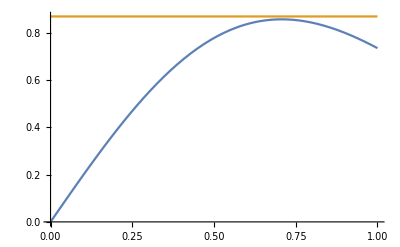

```mathematica
Plot[{Abs[prvi[x]],0.87},{x,0,1}]
```

```mathematica
m1=0.87
```

0.87

```mathematica
h=(b-a)/n//N
```

0.000227273

```mathematica
greska =(b-a)/2 m1*h
```

0.435/n

```mathematica
Solve[greska==10^-4,n]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n→4350.}}

```mathematica
n=4400
```

4400

```mathematica
h*Sum[f[a+i*h],{i,0,n-1}]
```

0.746896

Zadatak 3. Izračunati približno ∫_0^1 e^(-x^2)ⅆx složenom trapeznom formulom podelom intervala [0,1] na n=10 ekvidistantnih podintervala i oceniti grešku.

```mathematica
f[x_]=E^(-x^2);
```

```mathematica
a=0;b=1;n=10;
```

```mathematica
h=(b-a)/n//N;
```

```mathematica
prib = h/2*(f[a]+2*Sum[f[a+i*h],{i,1,n-1}]+f[b])
```

0.746211

```mathematica
drugi[x_]=D[f[x],{x,2}]
```

-2 ⅇ^(-x^2)+4 ⅇ^(-x^2) x^2

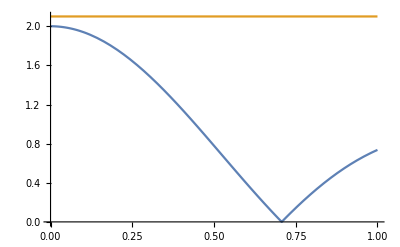

```mathematica
Plot[{Abs[drugi[x]],2.1},{x,0,1}]
```

```mathematica
m2=2.1
```

2.1

```mathematica
greska=(b-a)/12*m2*h^2
```

0.00175